# Elliptic Constraints

The plan is to build ellipsoidal constraints out of fully nonlinear constraints
	g_i(x)≥0	
The first thing to do is to build ellipsoidal constraints for a few linear constraints
	c_i+d_i.x≥0. 
The assumption is that we have an interior feasible point
	c_i+d_i.z>0 
and want to build an ellipsoidal constraint
	(x-z).B.(x-z)<Δ
entirely within the feasible set.

## 2 Constraints in 2D

Assuming the center point is at the origin.

{0.618723,0.208927}

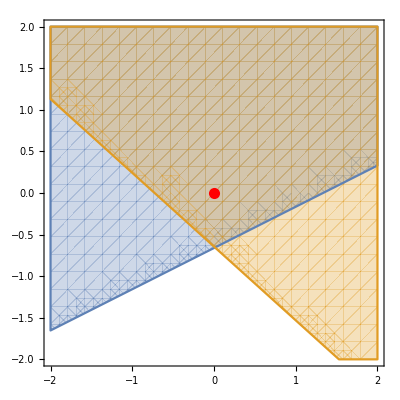

```mathematica
{c1,c2}=RandomReal[{0,1},2]
{d1,d2}=RandomReal[{-1,1},{2,2}];
RegionPlot[ {c1+d1.{x,y}>0, c1+d2.{x,y}>0}, {x,-2,2},{y,-2,2},
Epilog->{
{Red,PointSize[0.02],Point[{0,0}]}
}]
```

## 2D with pics

{{-0.661353,-0.847374}}

-0.514879

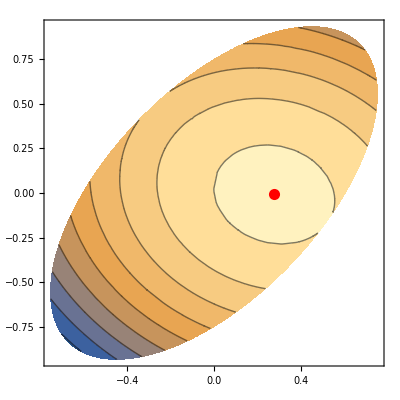

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
g=RandomReal[{-1,1},m];
Δ=0.7;
Ω=ImplicitRegion[{x,y}.B.{x,y}≤Δ^2,{x,y}];
{pStarBI}=NArgMin[{0.5*p.A.p+g.p,p.B.p≤Δ^2},p]
pCP=LinearSolve[A,-g];
M0=ArrayFlatten[({{{{Δ^2}}, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})];
M1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
M0Twiddle=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1Twiddle=ArrayFlatten[({{0, B}, {B, 0}})];
Max[Eigenvalues[{M0Twiddle,M1Twiddle}]]
ContourPlot[0.5*{x,y}.A.{x,y}+g.{x,y},{x,y}∈Ω,
Epilog->{{Red,PointSize[0.02],Point[pCP]}}]
```